```mathematica
ToString[#]&/@{Empty,Parsing,Parsed,Clearing,PreparingToLoad,Loading,Loaded,RequestingPlay,PreparingToPlay,WaitingForTrigger,Triggered,Playing,Pausing,Paused,Resuming,Stopping}
```

{Empty,Parsing,Parsed,Clearing,PreparingToLoad,Loading,Loaded,RequestingPlay,PreparingToPlay,WaitingForTrigger,Triggered,Playing,Pausing,Paused,Resuming,Stopping}

```mathematica
allStates={"Empty","Parsing","Parsed","Clearing","PreparingToLoad","Loading","Loaded","RequestingPlay","PreparingToPlay","WaitingForTrigger","Triggered","Playing","Pausing","Paused","Resuming","Stopping"};
```

```mathematica
transitions=
{
("Empty"->#&/@{"Parsing","Stopping"}),
("Parsing"->#&/@{"Parsed","Stopping"}),
("Parsed"->#&/@{"PreparingToLoad", "Clearing","Stopping"}),
("Clearing"->#&/@{"Empty"}),
("PreparingToLoad"->#&/@{"Loading","Stopping"}),
("Loading"->#&/@{"Loaded","Stopping"}),
("Loaded"->#&/@{"RequestingPlay","Parsed","Clearing","Stopping"}),
("RequestingPlay"->#&/@{"PreparingToPlay","Stopping"}),
("PreparingToPlay"->#&/@{"WaitingForTrigger","Stopping"}),
("WaitingForTrigger"->#&/@{"Triggered","Stopping"}),
("Triggered"->#&/@{"Playing","Stopping"}),
("Playing"->#&/@{"Pausing","WaitingForTrigger","Stopping"}),
("Pausing"->#&/@{"Paused","Stopping"}),
("Paused"->#&/@{"Resuming","Stopping"}),
("Resuming"->#&/@{"Playing","Stopping"}),
("Stopping"->#&/@{"Empty","Parsed","Loaded"})
};
Length[transitions]==Length[allStates]
```

True

```mathematica
{"SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","CircularEmbedding","RandomEmbedding","LinearEmbedding"}
```

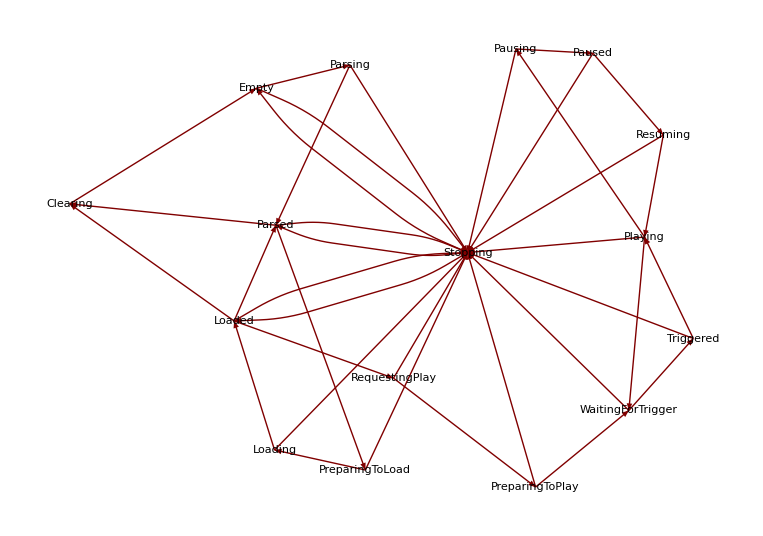

```mathematica
GraphPlot[transitions//Flatten//Sort,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,Method->"SpringEmbedding"]
```

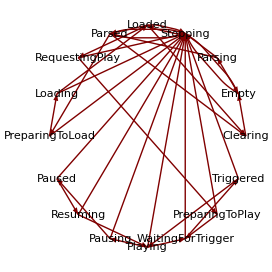

```mathematica
GraphPlot[transitions//Flatten//Sort,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,Method->"CircularEmbedding"]
```

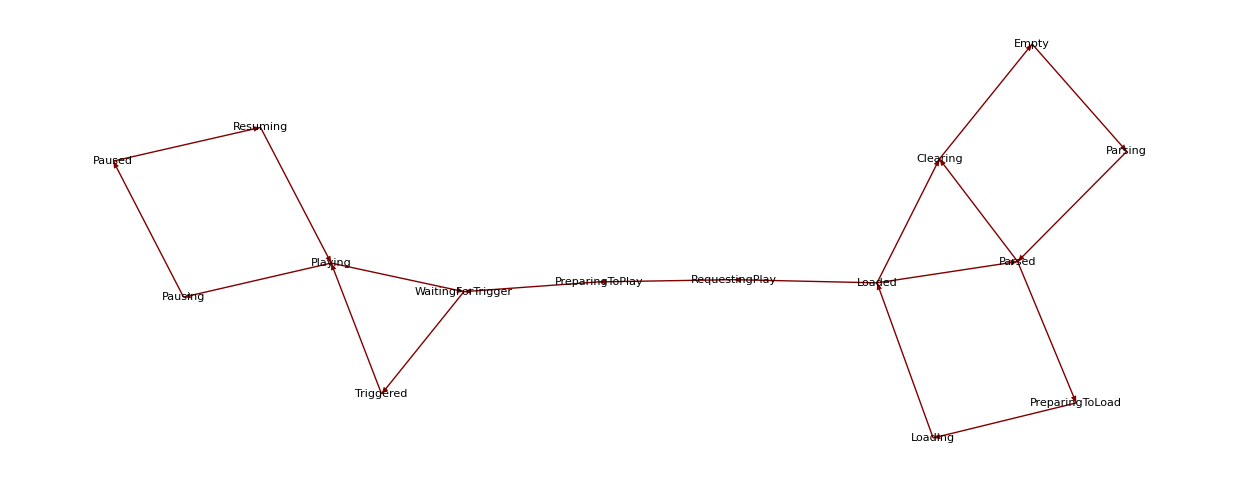

```mathematica
GraphPlot[DeleteCases[DeleteCases[(transitions//Flatten),a_->"Stopping"],"Stopping"->a_],VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,Method->"SpringEmbedding",BaseStyle->{FontSize->12}]
```

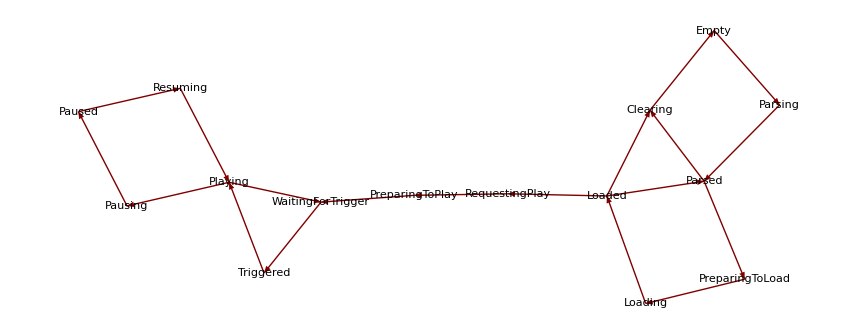

```mathematica
{"Layered","LayeredTop","LayeredLeft","ClosestPacking","ClosestPackingCenter","NestedGrid"}
```

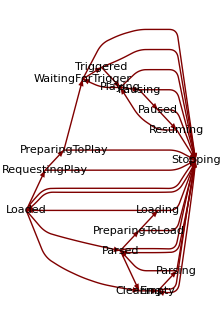

```mathematica
LayeredGraphPlot[transitions//Flatten,Left,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,PackingMethod->"NestedGrid",BaselinePosition->Top]
```

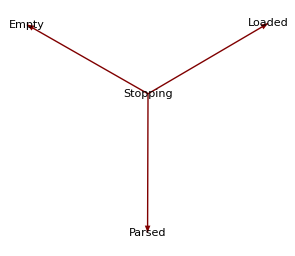

```mathematica
GraphPlot[("Stopping"->#&/@{"Empty","Parsed","Loaded"}),VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,Method->"SpringEmbedding",BaseStyle->{FontSize->12}]
```

```mathematica
Complement[transitions//Flatten,DeleteCases[DeleteCases[(transitions//Flatten),a_->"Stopping"],"Stopping"->a_]]
```

{Empty→Stopping,Loaded→Stopping,Loading→Stopping,Parsed→Stopping,Parsing→Stopping,Paused→Stopping,Pausing→Stopping,Playing→Stopping,PreparingToLoad→Stopping,PreparingToPlay→Stopping,RequestingPlay→Stopping,Resuming→Stopping,Stopping→Empty,Stopping→Loaded,Stopping→Parsed,Triggered→Stopping,WaitingForTrigger→Stopping}

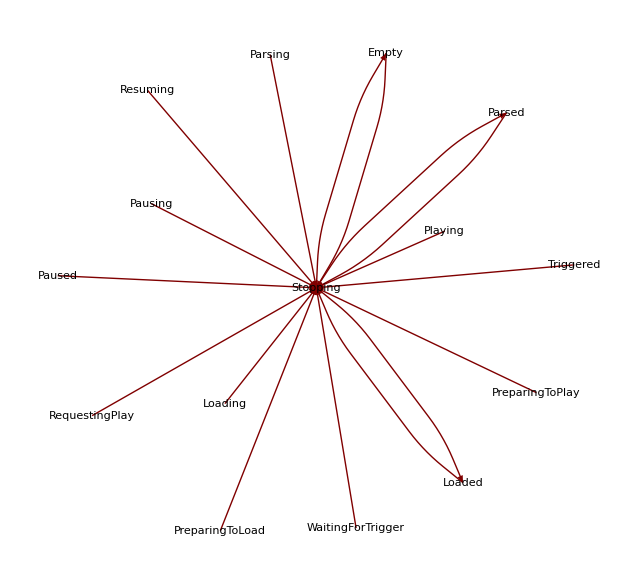

```mathematica
GraphPlot[Complement[transitions//Flatten,DeleteCases[DeleteCases[(transitions//Flatten),a_->"Stopping"],"Stopping"->a_]],VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->True,MultiedgeStyle->True,Method->"SpringEmbedding",BaseStyle->{FontSize->12}]
```